```mathematica
Plot3D[{Sin[x]^2-Sin[y]^2},{x,0,Pi},{y,0,Pi},ColorFunction->Function[{x,y,z},Hue[.65(1-z)]]]
```

-Graphics3D-

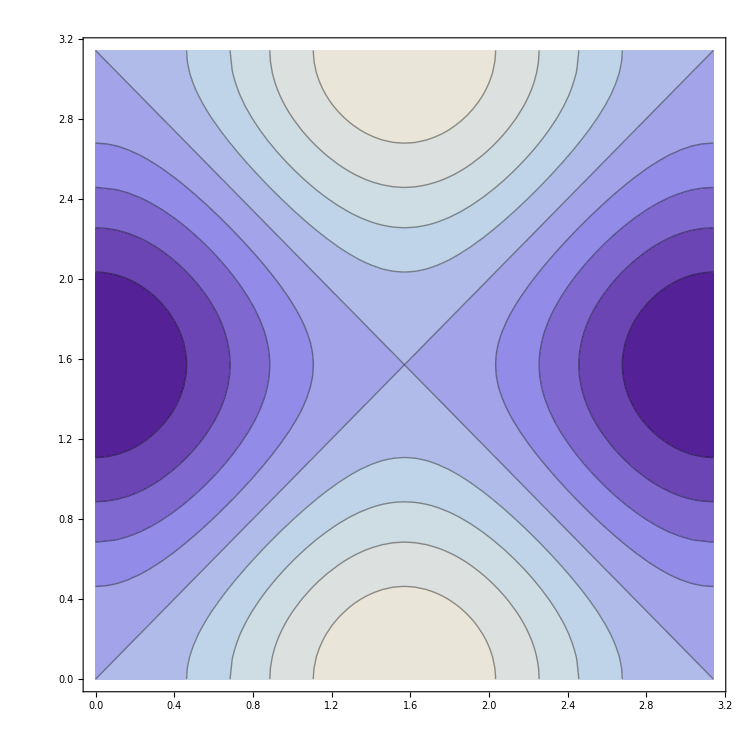

```mathematica
ContourPlot[{Sin[x]^2-Sin[y]^2},{x,0,Pi},{y,0,Pi}]
```

```mathematica
F[a_,x_]:=Integrate[Exp[-I m x]/Sin[m/a],{m,-Pi/a,Pi/a}]
```

```mathematica
F[0.1,5]
```

Integrate::idiv: Integral of ⅇ^-5 ⅈ m Csc[10.` m] does not converge on {-31.41592653589793`, 31.41592653589793`}.

∫_-31.4159^31.4159 ⅇ^(-5 ⅈ m) Csc[10. m]ⅆm